```mathematica
<<CompiledFunctionTools`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
densityPlotOptionsExport={PerformanceGoal->"Quality",PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
exportOptions={"AllowRasterization"->True,ImageSize->340,ImageResolution->800};
density3={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",PlotLegends->True,ImageSize->410};
```

## Defining the Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
as={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

{{-3/2-λ/4,-χ/(2 √3),-λ/(2 √3),0},{-χ/(2 √3),-1/2+1/3 (-(7 λ)/4-χ^2),-χ,-λ/(2 √3)},{-λ/(2 √3),-χ,1/2+1/3 (-(7 λ)/4-4 χ^2),-(5 χ)/(2 √3)},{0,-λ/(2 √3),-(5 χ)/(2 √3),3/2+1/3 (-(3 λ)/4-9 χ^2)}}

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(1/4 (-6-λ) | -χ/(2 √3) | -λ/(2 √3) | 0
-χ/(2 √3) | 1/12 (-6-7 λ-4 χ^2) | -χ | -λ/(2 √3)
-λ/(2 √3) | -χ | 1/12 (6-7 λ-16 χ^2) | -(5 χ)/(2 √3)
0 | -λ/(2 √3) | -(5 χ)/(2 √3) | 3/2-λ/4-3 χ^2)

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
sR[n_]:={1/(1-n),√(n/(2n-1))}
sL[n_]:=If[OddQ[n],{1-n/2,√(n/(n+2))},{1-n,√(n/(n+1))}]
```

```mathematica
{r1,r2}=sR[nn];
{l1,l2}=sL[nn];
derPiece[λ_?NumericQ,χ_?NumericQ]:=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[3+10/(0.8+(λ-r1)^2+(Abs[χ]-r2)^2)]+Round[3+10/(0.8+(λ-l1)^2+(Abs[χ]-l2)^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
```

## Ricci and Riemann

Ricci scalar for metric 2x2 is

```mathematica
R1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=derPieceC[λ,χ];
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/Det[g](g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=derPieceC[λ,χ];
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/Det[g](2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]
Ric[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms},
derTerms=derPieceC[λ,χ];
(ND[R1[l,χ],l,λ,Terms->derTerms]+ND[R2[λ,c],c,χ,Terms->derTerms])]
```

```mathematica
tabRic=Flatten[ParallelTable[{λ,χ,Ric[λ,χ]},{λ,-2,3,0.005},{χ,-1.5,1.5,0.005}],1]
```

$Aborted

```mathematica
Export[NotebookDirectory<>"N=3_Ricci.m",tabRic]
```

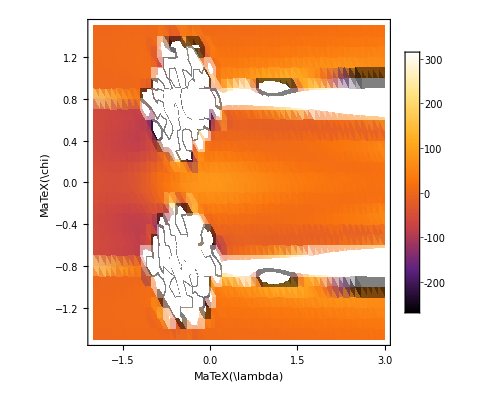

```mathematica
ListDensityPlot[tabRic,Evaluate@density3]
```